## transcripts init

```mathematica
firstBoardChar[s_String]:=StringMatchQ[StringTake[s,1],"/"|"|"|"\\"|"Y"|"J"|"K"]
```

```mathematica
readBoardsFromTranscript[f_]:=(
Reap[
id=StringDrop[StringDrop[f,11],-4];
Pint[id];
Catch[
While[True,
r=Read[f,String];
Which[
r===EndOfFile,Break[],
StringMatchQ[r,"generating partition #"~~__],(
p=StringCases[r,"generating partition #"~~p__:>p][[1]];
Pint["partition "<>p];
r=Read[f,String];
Which[
StringMatchQ[r,"idhash "~~__~~"hardest is "~~(NumberString)~~__],(
moves=StringCases[r,"idhash "~~__~~"hardest is "~~m:NumberString~~__:>m][[1]];
board=Read[f,{String,String,String,String,String,String,String,String}];
If[And@@(firstBoardChar/@board),Sow[{{"id"->id,"partition"->p,"moves"->moves},board}],Throw[{"not a board",board},1]]
),
StringMatchQ[r,"idhash "~~__~~"hardest is null"~~__],Null,
True,Throw[{"1",r},1]
]
)
]
]
,
1
,
Print["bad",#]&
];
Close[f];
Null
][[2,1]]
)
```

## data

```mathematica
counts={#,Flatten[StringCases[ReadList[#,String],"hardest is "~~Shortest[a__]~~" moves":>ToExpression[a]]]}&/@transcriptFileNames;
```

```mathematica
Sort[Flatten[counts[[All,2]]]]
```

{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,«50964»,62,62,62,62,62,62,62,62,63,63,63,63,63,63,63,63,63,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,65,65,65,65,65,65,65,65,65,65,65,65,66,66,66,66,66,66,66,66,66,66,66,67,67,67,67,67,67,67,67,67,67,68,68,68,68,68,69,69,69,70,70,70,71,71,71,71,71,71,71,71,71,71,72,72,73,73,74,74,74,74,74,74,74,74,75,75,76,76,76,76,76,76,76,77,77,77,77,78,78,78,78,81,81,82,82,82,84,85,85,87,87,88,89,89,90,99}

```mathematica
Total[Length[#[[2]]]&/@counts]
```

51234

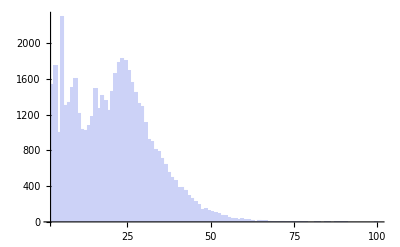

```mathematica
Histogram[Flatten[counts[[All,2]]]]
```

## generate .dat file name and contents from transcript

```mathematica
generateDatFileNamesAndContents[transcript_]:=
(
boards=readBoardsFromTranscript[transcript];
(
rules=#[[1]];
data=#[[2]];
file="gen-"<>("id"/.rules)<>"-"<>("partition"/.rules)<>".dat";
{file,"moves: "<>("moves"/.rules)<>"\n"<>StringJoin[((ToString[#]<>"\n")&/@data)]}
)&/@boards
)
```

## generate episode 1 zip file

```mathematica
SetDirectory["C:\\Users\\brenton\\Documents\\Github\\Deadlock\\transcripts\\"];
```

```mathematica
transcriptFileNames=FileNames["transcript-*.txt",""];
```

```mathematica
a=generateDatFileNamesAndContents[#]&/@transcriptFileNames;
```

```mathematica
b=Flatten[a,1];
```

```mathematica
b=SortBy[b,StringReplace[#[[2]],"moves: "~~m:NumberString~~__:>ToExpression[m]]&];
```

```mathematica
Length[b]
```

51234

```mathematica
c=Select[b,ToExpression[StringReplace[#[[2]],"moves: "~~m:NumberString~~__:>m]]≥10&];
```

```mathematica
Length[c]
```

38892

```mathematica
c[[1]]
```

{gen-0-4-3-1.dat,moves: 10
/J-----\
YA  BRR|
|A  B C|
|A  B CJ
|D    C|
|D     |
|D     |
\------/
}

```mathematica
dist=0;
besti;
bestj;
While[True,
i=RandomInteger[{1,Length[c]}];
j=RandomInteger[{1,Length[c]}];
If[i==j,Continue[]];
d=HammingDistance[c[[i,2]],c[[j,2]]];
If[d>dist,
besti=i;
bestj=j;
dist=d
]
]
```

$Aborted

```mathematica
Dynamic[dist]
```

```mathematica
{c[[besti,2]],c[[bestj,2]]}
```

{moves: 29
/-J-K--\
|  AA  |
|   BBB|
J      K
|CCDD  |
|EEER  |
|FFFR  |
\-Y----/
,moves: 34
/---Y--\
|ABCDDD|
|ABC  E|
|ABFFFE|
|    GE|
|    GR|
K    GRJ
\---K-J/
}

```mathematica
d=Take[c,100];
```

```mathematica
Length[d]
```

194

```mathematica
AbsoluteTiming[Export["C:\\Users\\brenton\\Documents\\Github\\Deadlock\\BypassResources\\gen\\episode1.zip",d[[All,2]]~Join~{Length[d]},{"ZIP",({#,"Text"}&/@d[[All,1]])~Join~{{"metadata.txt","Text"}}}]]
```

{2.75606,C:\Users\brenton\Documents\Github\Deadlock\BypassResources\gen\episode1.zip}

## generate tutorial zip file

```mathematica
SetDirectory["C:\\Users\\brenton\\Documents\\Github\\Deadlock\\Bypass\\src\\main\\dat\\tutorial\\"];
```

```mathematica
tutorialFileNames=FileNames["tut-*.dat",""];
```

```mathematica
d={#,Import[#,"Text"]}&/@tutorialFileNames;
```

```mathematica
AbsoluteTiming[Export["C:\\Users\\brenton\\Documents\\Github\\Deadlock\\BypassResources\\gen\\tutorial.zip",d[[All,2]]~Join~{Length[d]},{"ZIP",({#,"Text"}&/@d[[All,1]])~Join~{{"metadata.txt","Text"}}}]]
```

{0.13515,C:\Users\brenton\Documents\Github\Deadlock\BypassResources\gen\tutorial.zip}